```mathematica
mySets=Take[Keys[allGraphs5],100]
```

{0,19683,26244,28431,29160,29403,29484,29511,29520,29523,29524,29525,29527,29521,29529,29533,29537,29514,29515,29517,29512,29513,29542,29551,29560,29493,29496,29497,29494,29502,29506,29487,29488,29485,29574,29602,29605,29608,29633,29577,29430,29439,29442,29443,29446,29440,29433,29434,29436,29431,29460,29469,29412,29415,29416,29417,29413,29406,29407,29404,29405,29646,29736,29766,29767,29768,29797,29737,29826,29857,29888,29676,29677,29706,29647,29648,29241,29268,29277,29280,29281,29282,29278,29271,29272,29269,29270,29296,29305,29250,29253,29254,29257,29251,29244,29245,29247,29242,29322,29350}

```mathematica
all=Monitor[Flatten[Table[{ChromaticPolynomial[allGraphs5[mySets[[k]],"graph"],x]*ChromaticPolynomial[allGraphs5[mySets[[l]],"graph"],x],k+1,l},{k,Length[mySets]},{l,k,Length[mySets]}],1],{k,l}]
```

{{x^10,2,1},{x^5 (-x^4+x^5),2,2},{x^5 (x^3-2 x^4+x^5),2,3},{x^5 (-x^2+3 x^3-3 x^4+x^5),2,4},{x^5 (x-4 x^2+6 x^3-4 x^4+x^5),2,5},{x^5 (2 x-7 x^2+9 x^3-5 x^4+x^5),2,6},{x^5 (4 x-12 x^2+13 x^3-6 x^4+x^5),2,7},{x^5 (8 x-20 x^2+18 x^3-7 x^4+x^5),2,8},{x^5 (12 x-28 x^2+23 x^3-8 x^4+x^5),2,9},{x^5 (18 x-39 x^2+29 x^3-9 x^4+x^5),2,10},{x^5 (24 x-50 x^2+35 x^3-10 x^4+x^5),2,11},{x^5 (-6 x+11 x^2-6 x^3+x^4),2,12},{x^5 (-6 x+11 x^2-6 x^3+x^4),2,13},5025,{(-x+3 x^2-3 x^3+x^4) (8 x-20 x^2+18 x^3-7 x^4+x^5),97,99},{(-2 x+5 x^2-4 x^3+x^4) (8 x-20 x^2+18 x^3-7 x^4+x^5),97,100},{(-2 x+5 x^2-4 x^3+x^4)^2,98,97},{(-2 x+5 x^2-4 x^3+x^4) (4 x-12 x^2+13 x^3-6 x^4+x^5),98,98},{(-2 x+5 x^2-4 x^3+x^4) (-x+3 x^2-3 x^3+x^4),98,99},{(-2 x+5 x^2-4 x^3+x^4)^2,98,100},{(4 x-12 x^2+13 x^3-6 x^4+x^5)^2,99,98},{(-x+3 x^2-3 x^3+x^4) (4 x-12 x^2+13 x^3-6 x^4+x^5),99,99},{(-2 x+5 x^2-4 x^3+x^4) (4 x-12 x^2+13 x^3-6 x^4+x^5),99,100},{(-x+3 x^2-3 x^3+x^4)^2,100,99},{(-2 x+5 x^2-4 x^3+x^4) (-x+3 x^2-3 x^3+x^4),100,100},{(-2 x+5 x^2-4 x^3+x^4)^2,101,100}}
 |  |  |  |

```mathematica
DeleteDuplicates[Map[Expand[First[#]]&,all]]
```

{x^10,-x^9+x^10,x^8-2 x^9+x^10,-x^7+3 x^8-3 x^9+x^10,x^6-4 x^7+6 x^8-4 x^9+x^10,2 x^6-7 x^7+9 x^8-5 x^9+x^10,4 x^6-12 x^7+13 x^8-6 x^9+x^10,8 x^6-20 x^7+18 x^8-7 x^9+x^10,12 x^6-28 x^7+23 x^8-8 x^9+x^10,18 x^6-39 x^7+29 x^8-9 x^9+x^10,24 x^6-50 x^7+35 x^8-10 x^9+x^10,-6 x^6+11 x^7-6 x^8+x^9,-4 x^6+8 x^7-5 x^8+x^9,2 x^6-3 x^7+x^8,6 x^6-17 x^7+17 x^8-7 x^9+x^10,-2 x^6+5 x^7-4 x^8+x^9,14 x^6-31 x^7+24 x^8-8 x^9+x^10,-x^6+3 x^7-3 x^8+x^9,x^6-2 x^7+x^8,-x^6+x^7,-x^5+5 x^6-10 x^7+10 x^8-5 x^9+x^10,-2 x^5+9 x^6-16 x^7+14 x^8-6 x^9+x^10,-4 x^5+16 x^6-25 x^7+19 x^8-7 x^9+x^10,-8 x^5+28 x^6-38 x^7+25 x^8-8 x^9+x^10,-12 x^5+40 x^6-51 x^7+31 x^8-9 x^9+x^10,-18 x^5+57 x^6-68 x^7+38 x^8-10 x^9+x^10,-24 x^5+74 x^6-85 x^7+45 x^8-11 x^9+x^10,6 x^5-17 x^6+17 x^7-7 x^8+x^9,4 x^5-12 x^6+13 x^7-6 x^8+x^9,-2 x^5+5 x^6-4 x^7+x^8,-6 x^5+23 x^6-34 x^7+24 x^8-8 x^9+x^10,2 x^5-7 x^6+9 x^7-5 x^8+x^9,-14 x^5+45 x^6-55 x^7+32 x^8-9 x^9+x^10,x^5-4 x^6+6 x^7-4 x^8+x^9,-x^5+3 x^6-3 x^7+x^8,x^5-2 x^6+x^7,x^4-6 x^5+15 x^6-20 x^7+15 x^8-6 x^9+x^10,2 x^4-11 x^5+25 x^6-30 x^7+20 x^8-7 x^9+x^10,4 x^4-20 x^5+41 x^6-44 x^7+26 x^8-8 x^9+x^10,8 x^4-36 x^5+66 x^6-63 x^7+33 x^8-9 x^9+x^10,12 x^4-52 x^5+91 x^6-82 x^7+40 x^8-10 x^9+x^10,18 x^4-75 x^5+125 x^6-106 x^7+48 x^8-11 x^9+x^10,24 x^4-98 x^5+159 x^6-130 x^7+56 x^8-12 x^9+x^10,-6 x^4+23 x^5-34 x^6+24 x^7-8 x^8+x^9,-4 x^4+16 x^5-25 x^6+19 x^7-7 x^8+x^9,2 x^4-7 x^5+9 x^6-5 x^7+x^8,6 x^4-29 x^5+57 x^6-58 x^7+32 x^8-9 x^9+x^10,-2 x^4+9 x^5-16 x^6+14 x^7-6 x^8+x^9,14 x^4-59 x^5+100 x^6-87 x^7+41 x^8-10 x^9+x^10,-x^4+5 x^5-10 x^6+10 x^7-5 x^8+x^9,x^4-4 x^5+6 x^6-4 x^7+x^8,-x^4+3 x^5-3 x^6+x^7,-x^3+7 x^4-21 x^5+35 x^6-35 x^7+21 x^8-7 x^9+x^10,-2 x^3+13 x^4-36 x^5+55 x^6-50 x^7+27 x^8-8 x^9+x^10,-4 x^3+24 x^4-61 x^5+85 x^6-70 x^7+34 x^8-9 x^9+x^10,-8 x^3+44 x^4-102 x^5+129 x^6-96 x^7+42 x^8-10 x^9+x^10,-12 x^3+64 x^4-143 x^5+173 x^6-122 x^7+50 x^8-11 x^9+x^10,-18 x^3+93 x^4-200 x^5+231 x^6-154 x^7+59 x^8-12 x^9+x^10,-24 x^3+122 x^4-257 x^5+289 x^6-186 x^7+68 x^8-13 x^9+x^10,6 x^3-29 x^4+57 x^5-58 x^6+32 x^7-9 x^8+x^9,4 x^3-20 x^4+41 x^5-44 x^6+26 x^7-8 x^8+x^9,-2 x^3+9 x^4-16 x^5+14 x^6-6 x^7+x^8,-6 x^3+35 x^4-86 x^5+115 x^6-90 x^7+41 x^8-10 x^9+x^10,2 x^3-11 x^4+25 x^5-30 x^6+20 x^7-7 x^8+x^9,-14 x^3+73 x^4-159 x^5+187 x^6-128 x^7+51 x^8-11 x^9+x^10,x^3-6 x^4+15 x^5-20 x^6+15 x^7-6 x^8+x^9,-x^3+5 x^4-10 x^5+10 x^6-5 x^7+x^8,x^3-4 x^4+6 x^5-4 x^6+x^7,x^2-8 x^3+28 x^4-56 x^5+70 x^6-56 x^7+28 x^8-8 x^9+x^10,2 x^2-15 x^3+49 x^4-91 x^5+105 x^6-77 x^7+35 x^8-9 x^9+x^10,4 x^2-28 x^3+85 x^4-146 x^5+155 x^6-104 x^7+43 x^8-10 x^9+x^10,8 x^2-52 x^3+146 x^4-231 x^5+225 x^6-138 x^7+52 x^8-11 x^9+x^10,12 x^2-76 x^3+207 x^4-316 x^5+295 x^6-172 x^7+61 x^8-12 x^9+x^10,18 x^2-111 x^3+293 x^4-431 x^5+385 x^6-213 x^7+71 x^8-13 x^9+x^10,24 x^2-146 x^3+379 x^4-546 x^5+475 x^6-254 x^7+81 x^8-14 x^9+x^10,-6 x^2+35 x^3-86 x^4+115 x^5-90 x^6+41 x^7-10 x^8+x^9,-4 x^2+24 x^3-61 x^4+85 x^5-70 x^6+34 x^7-9 x^8+x^9,2 x^2-11 x^3+25 x^4-30 x^5+20 x^6-7 x^7+x^8,6 x^2-41 x^3+121 x^4-201 x^5+205 x^6-131 x^7+51 x^8-11 x^9+x^10,-2 x^2+13 x^3-36 x^4+55 x^5-50 x^6+27 x^7-8 x^8+x^9,14 x^2-87 x^3+232 x^4-346 x^5+315 x^6-179 x^7+62 x^8-12 x^9+x^10,-x^2+7 x^3-21 x^4+35 x^5-35 x^6+21 x^7-7 x^8+x^9,x^2-6 x^3+15 x^4-20 x^5+15 x^6-6 x^7+x^8,-x^2+5 x^3-10 x^4+10 x^5-5 x^6+x^7,16 x^2-96 x^3+248 x^4-360 x^5+321 x^6-180 x^7+62 x^8-12 x^9+x^10,24 x^2-140 x^3+350 x^4-489 x^5+417 x^6-222 x^7+72 x^8-13 x^9+x^10,36 x^2-204 x^3+493 x^4-662 x^5+539 x^6-272 x^7+83 x^8-14 x^9+x^10,48 x^2-268 x^3+636 x^4-835 x^5+661 x^6-322 x^7+94 x^8-15 x^9+x^10,-12 x^2+64 x^3-143 x^4+173 x^5-122 x^6+50 x^7-11 x^8+x^9,-8 x^2+44 x^3-102 x^4+129 x^5-96 x^6+42 x^7-10 x^8+x^9,4 x^2-20 x^3+41 x^4-44 x^5+26 x^6-8 x^7+x^8,28 x^2-160 x^3+391 x^4-533 x^5+443 x^6-230 x^7+73 x^8-13 x^9+x^10,-2 x^2+9 x^3-16 x^4+14 x^5-6 x^6+x^7,32 x^2-176 x^3+416 x^4-552 x^5+450 x^6-231 x^7+73 x^8-13 x^9+x^10,48 x^2-256 x^3+584 x^4-744 x^5+579 x^6-282 x^7+84 x^8-14 x^9+x^10,72 x^2-372 x^3+818 x^4-999 x^5+741 x^6-342 x^7+96 x^8-15 x^9+x^10,96 x^2-488 x^3+1052 x^4-1254 x^5+903 x^6-402 x^7+108 x^8-16 x^9+x^10,-24 x^2+116 x^3-234 x^4+255 x^5-162 x^6+60 x^7-12 x^8+x^9,-16 x^2+80 x^3-168 x^4+192 x^5-129 x^6+51 x^7-11 x^8+x^9,8 x^2-36 x^3+66 x^4-63 x^5+33 x^6-9 x^7+x^8,56 x^2-292 x^3+650 x^4-807 x^5+612 x^6-291 x^7+85 x^8-14 x^9+x^10,-4 x^2+16 x^3-25 x^4+19 x^5-7 x^6+x^7,64 x^2-320 x^3+688 x^4-832 x^5+620 x^6-292 x^7+85 x^8-14 x^9+x^10,96 x^2-464 x^3+960 x^4-1112 x^5+790 x^6-353 x^7+97 x^8-15 x^9+x^10,144 x^2-672 x^3+1336 x^4-1480 x^5+1001 x^6-424 x^7+110 x^8-16 x^9+x^10,192 x^2-880 x^3+1712 x^4-1848 x^5+1212 x^6-495 x^7+123 x^8-17 x^9+x^10,-48 x^2+208 x^3-376 x^4+368 x^5-211 x^6+71 x^7-13 x^8+x^9,-32 x^2+144 x^3-272 x^4+280 x^5-170 x^6+61 x^7-12 x^8+x^9,16 x^2-64 x^3+104 x^4-88 x^5+41 x^6-10 x^7+x^8,112 x^2-528 x^3+1064 x^4-1200 x^5+831 x^6-363 x^7+98 x^8-15 x^9+x^10,-8 x^2+28 x^3-38 x^4+25 x^5-8 x^6+x^7,216 x^2-972 x^3+1854 x^4-1961 x^5+1261 x^6-506 x^7+124 x^8-17 x^9+x^10,288 x^2-1272 x^3+2372 x^4-2442 x^5+1521 x^6-588 x^7+138 x^8-18 x^9+x^10,-72 x^2+300 x^3-518 x^4+481 x^5-260 x^6+82 x^7-14 x^8+x^9,24 x^2-92 x^3+142 x^4-113 x^5+49 x^6-11 x^7+x^8,168 x^2-764 x^3+1478 x^4-1593 x^5+1050 x^6-435 x^7+111 x^8-16 x^9+x^10,12 x^2-52 x^3+91 x^4-82 x^5+40 x^6-10 x^7+x^8,-12 x^2+40 x^3-51 x^4+31 x^5-9 x^6+x^7,324 x^2-1404 x^3+2565 x^4-2586 x^5+1579 x^6-600 x^7+139 x^8-18 x^9+x^10,432 x^2-1836 x^3+3276 x^4-3211 x^5+1897 x^6-694 x^7+154 x^8-19 x^9+x^10,-108 x^2+432 x^3-711 x^4+625 x^5-318 x^6+94 x^7-15 x^8+x^9,36 x^2-132 x^3+193 x^4-144 x^5+58 x^6-12 x^7+x^8,108 x^2-540 x^3+1143 x^4-1336 x^5+943 x^6-412 x^7+109 x^8-16 x^9+x^10,-36 x^2+168 x^3-325 x^4+337 x^5-202 x^6+70 x^7-13 x^8+x^9,252 x^2-1104 x^3+2047 x^4-2105 x^5+1319 x^6-518 x^7+125 x^8-17 x^9+x^10,-18 x^2+93 x^3-200 x^4+231 x^5-154 x^6+59 x^7-12 x^8+x^9,18 x^2-75 x^3+125 x^4-106 x^5+48 x^6-11 x^7+x^8,-18 x^2+57 x^3-68 x^4+38 x^5-10 x^6+x^7,576 x^2-2400 x^3+4180 x^4-3980 x^5+2273 x^6-800 x^7+170 x^8-20 x^9+x^10,-144 x^2+564 x^3-904 x^4+769 x^5-376 x^6+106 x^7-16 x^8+x^9,-96 x^2+392 x^3-660 x^4+594 x^5-309 x^6+93 x^7-15 x^8+x^9,48 x^2-172 x^3+244 x^4-175 x^5+67 x^6-13 x^7+x^8,144 x^2-708 x^3+1468 x^4-1673 x^5+1145 x^6-482 x^7+122 x^8-17 x^9+x^10,-48 x^2+220 x^3-416 x^4+419 x^5-242 x^6+80 x^7-14 x^8+x^9,336 x^2-1444 x^3+2616 x^4-2617 x^5+1588 x^6-601 x^7+139 x^8-18 x^9+x^10,-24 x^2+122 x^3-257 x^4+289 x^5-186 x^6+68 x^7-13 x^8+x^9,24 x^2-98 x^3+159 x^4-130 x^5+56 x^6-12 x^7+x^8,-24 x^2+74 x^3-85 x^4+45 x^5-11 x^6+x^7,-84 x^2+340 x^3-569 x^4+512 x^5-269 x^6+83 x^7-14 x^8+x^9,6 x^2-29 x^3+57 x^4-58 x^5+32 x^6-9 x^7+x^8,-6 x^2+23 x^3-34 x^4+24 x^5-8 x^6+x^7,6 x^2-17 x^3+17 x^4-7 x^5+x^6,-56 x^2+236 x^3-414 x^4+393 x^5-219 x^6+72 x^7-13 x^8+x^9,4 x^2-12 x^3+13 x^4-6 x^5+x^6,28 x^2-104 x^3+155 x^4-119 x^5+50 x^6-11 x^7+x^8,2 x^2-7 x^3+9 x^4-5 x^5+x^6,-2 x^2+5 x^3-4 x^4+x^5,84 x^2-424 x^3+909 x^4-1081 x^5+781 x^6-352 x^7+97 x^8-15 x^9+x^10,-28 x^2+132 x^3-259 x^4+274 x^5-169 x^6+61 x^7-12 x^8+x^9,196 x^2-868 x^3+1633 x^4-1712 x^5+1100 x^6-446 x^7+112 x^8-16 x^9+x^10,-14 x^2+73 x^3-159 x^4+187 x^5-128 x^6+51 x^7-11 x^8+x^9,14 x^2-59 x^3+100 x^4-87 x^5+41 x^6-10 x^7+x^8,-14 x^2+45 x^3-55 x^4+32 x^5-9 x^6+x^7,x^2-4 x^3+6 x^4-4 x^5+x^6,-x^2+3 x^3-3 x^4+x^5,x^2-2 x^3+x^4}

```mathematica
Last[DeleteDuplicates[Map[Expand[First[#]]&,all]]]
```

x^2-2 x^3+x^4

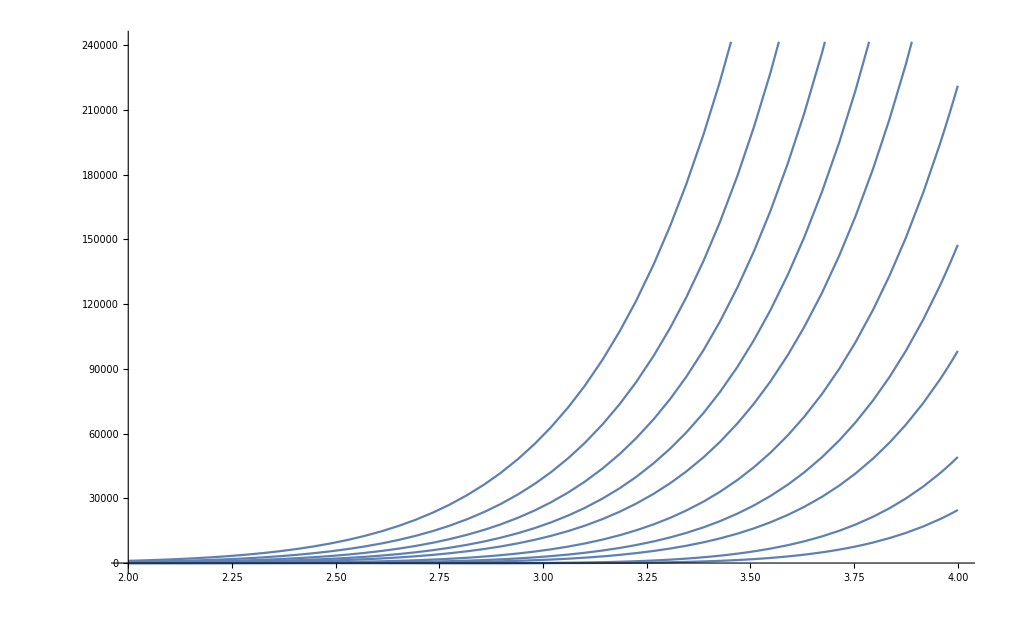

```mathematica
Plot[Take[DeleteDuplicates[Map[Expand[First[#]]&,all]],10],{x,2,4}]
```

```mathematica
With[{poly=DeleteDuplicates[Map[Expand[First[#]]&,all]]},Select[Keys[allGraphs5],ConnectedGraphQ[allGraphs5[#,"graph"]]&&MemberQ[poly,Expand[ChromaticPolynomial[allGraphs5[#,"graph"],x]]]&]]
```

{}

```mathematica
Table[ShowGraph5Least[k],{k,{28431,28674,28917,28512,28593,28440,28449,30708,26973,27216,27459,27000,27027,26976,26979,27732,26568,26514,26496,26490,26488,26820,26760,26731,26325,26271,26253,26247,26245,26246,35244,33780,33129,33075,33049,22599,22680,22761,22626,22653,22600,22601,23356,22113,22194,22284,21978,21960,21954,21952,22060,22035,21897,21879,21873,21876,21871,24868,24381,24165,24141,20655,20682,20712,20493,20520,20548,20448,20442,20440,20475,20421,20430,20415,20413,21411,21249,21177,20007,20016,20025,19953,19956,19959,19935,19929,19927,19928,19791,19792,19793,19773,19767,19770,19765,19719,19728,19713,19711,19695,19696,19697,19699,19693,19705,19687,48438,46926,46179,46173,46171,42390,41643,41637,41635,40131,40125,40123,39378,39376,39370,9477,9486,9495,9480,9483,9478,9479,10210,8991,9090,9000,8829,8838,8775,8784,8793,8802,8760,8758,8770,8751,8749,11674,11187,10971,10947,7533,7566,7536,7371,7374,7377,7452,7317,7320,7299,7302,7306,7294,7291,8265,8103,8031,6885,6894,6975,6831,6834,6861,6813,6807,6805,6806,6669,6670,6671,6697,6651,6645,6643,6751,6726,6597,6591,6589,6624,6573,6574,6575,6571,6565,16050,15399,15345,15319,13935,13881,13855,13230,13204,13150,3159,3160,3161,3402,2997,3026,2998,2943,2944,2925,2930,2926,2919,2920,3889,3727,3655,2511,2520,2457,2460,2463,2487,2439,2433,2431,2763,2703,2674,2295,2296,2323,2277,2271,2274,2269,2223,2217,2215,2250,2199,2200,2203,2197,2191,5347,5131,5107,4644,4620,4404,1053,1062,1071,1143,999,1002,981,975,973,1305,1245,1216,837,838,819,813,811,919,894,765,774,759,757,741,742,739,751,733,1782,1710,1548,351,360,369,354,357,352,353,382,336,334,346,327,325,442,417,279,282,286,274,271,309,255,256,257,253,247,606,577,517,117,122,118,111,112,145,93,94,97,91,85,193,39,40,37,49,31}}]
```

{-Graphics-2843112,-Graphics-286746,-Graphics-289176,-Graphics-285126,-Graphics-285933,-Graphics-284406,-Graphics-284496,-Graphics-307084,-Graphics-2697310,-Graphics-272165,-Graphics-274595,-Graphics-270005,-Graphics-270272,-Graphics-269766,-Graphics-269794,-Graphics-277326,-Graphics-265685,-Graphics-265145,-Graphics-264965,-Graphics-264906,-Graphics-264885,-Graphics-268205,-Graphics-267606,-Graphics-267315,-Graphics-2632510,-Graphics-2627111,-Graphics-2625310,-Graphics-2624712,-Graphics-2624510,-Graphics-262466,-Graphics-352443,-Graphics-337803,-Graphics-331292,-Graphics-330752,-Graphics-330493,-Graphics-2259910,-Graphics-226806,-Graphics-227614,-Graphics-226265,-Graphics-226532,-Graphics-226005,-Graphics-226015,-Graphics-233565,-Graphics-221139,-Graphics-221946,-Graphics-222843,-Graphics-219786,-Graphics-219606,-Graphics-219545,-Graphics-219526,-Graphics-220604,-Graphics-220353,-Graphics-2189710,-Graphics-218799,-Graphics-2187310,-Graphics-218763,-Graphics-2187110,-Graphics-248683,-Graphics-243814,-Graphics-241653,-Graphics-241413,-Graphics-206558,-Graphics-206825,-Graphics-207123,-Graphics-204939,-Graphics-205206,-Graphics-205483,-Graphics-204485,-Graphics-204426,-Graphics-204405,-Graphics-204753,-Graphics-204218,-Graphics-204305,-Graphics-204159,-Graphics-204138,-Graphics-214115,-Graphics-212496,-Graphics-211775,-Graphics-2000710,-Graphics-200165,-Graphics-200255,-Graphics-1995310,-Graphics-199566,-Graphics-199594,-Graphics-199358,-Graphics-199299,-Graphics-199278,-Graphics-199285,-Graphics-1979112,-Graphics-197926,-Graphics-197936,-Graphics-1977310,-Graphics-1976710,-Graphics-197703,-Graphics-197659,-Graphics-1971910,-Graphics-197286,-Graphics-1971312,-Graphics-1971110,-Graphics-1969510,-Graphics-196965,-Graphics-196975,-Graphics-196993,-Graphics-196938,-Graphics-197055,-Graphics-1968710,-Graphics-484386,-Graphics-469265,-Graphics-461795,-Graphics-461736,-Graphics-461715,-Graphics-423906,-Graphics-416436,-Graphics-416376,-Graphics-416356,-Graphics-401315,-Graphics-401256,-Graphics-401235,-Graphics-393786,-Graphics-393765,-Graphics-393706,-Graphics-947712,-Graphics-94866,-Graphics-94956,-Graphics-94806,-Graphics-94833,-Graphics-94786,-Graphics-94796,-Graphics-102106,-Graphics-899112,-Graphics-90906,-Graphics-90006,-Graphics-882912,-Graphics-88386,-Graphics-877511,-Graphics-87845,-Graphics-87936,-Graphics-88023,-Graphics-87606,-Graphics-87586,-Graphics-87706,-Graphics-875112,-Graphics-874912,-Graphics-116743,-Graphics-111874,-Graphics-109713,-Graphics-109473,-Graphics-753310,-Graphics-75664,-Graphics-75366,-Graphics-737110,-Graphics-73745,-Graphics-73773,-Graphics-74523,-Graphics-731710,-Graphics-73206,-Graphics-72999,-Graphics-73026,-Graphics-73063,-Graphics-72946,-Graphics-72919,-Graphics-82656,-Graphics-81036,-Graphics-80316,-Graphics-688511,-Graphics-68945,-Graphics-69752,-Graphics-683110,-Graphics-68346,-Graphics-68613,-Graphics-681310,-Graphics-680712,-Graphics-680510,-Graphics-68066,-Graphics-666911,-Graphics-66705,-Graphics-66716,-Graphics-66973,-Graphics-665110,-Graphics-664511,-Graphics-664310,-Graphics-67513,-Graphics-67263,-Graphics-659710,-Graphics-659112,-Graphics-658910,-Graphics-66243,-Graphics-657312,-Graphics-65746,-Graphics-65756,-Graphics-65719,-Graphics-656512,-Graphics-160504,-Graphics-153993,-Graphics-153453,-Graphics-153194,-Graphics-139353,-Graphics-138813,-Graphics-138554,-Graphics-132303,-Graphics-132043,-Graphics-131503,-Graphics-315910,-Graphics-31605,-Graphics-31615,-Graphics-34026,-Graphics-299712,-Graphics-30266,-Graphics-29986,-Graphics-294311,-Graphics-29445,-Graphics-292510,-Graphics-29305,-Graphics-29265,-Graphics-291910,-Graphics-29205,-Graphics-38895,-Graphics-37276,-Graphics-36555,-Graphics-251112,-Graphics-25206,-Graphics-245710,-Graphics-24605,-Graphics-24633,-Graphics-24873,-Graphics-24399,-Graphics-243310,-Graphics-243110,-Graphics-27636,-Graphics-27036,-Graphics-26746,-Graphics-229512,-Graphics-22966,-Graphics-23233,-Graphics-227712,-Graphics-227111,-Graphics-22743,-Graphics-226912,-Graphics-222310,-Graphics-221711,-Graphics-221510,-Graphics-22503,-Graphics-219910,-Graphics-22005,-Graphics-22032,-Graphics-219710,-Graphics-219111,-Graphics-53473,-Graphics-51312,-Graphics-51072,-Graphics-46443,-Graphics-46203,-Graphics-44043,-Graphics-105310,-Graphics-10625,-Graphics-10715,-Graphics-11433,-Graphics-99910,-Graphics-10026,-Graphics-9818,-Graphics-9759,-Graphics-9738,-Graphics-13055,-Graphics-12456,-Graphics-12165,-Graphics-83712,-Graphics-8386,-Graphics-81910,-Graphics-81310,-Graphics-8119,-Graphics-9194,-Graphics-8943,-Graphics-76510,-Graphics-7746,-Graphics-75912,-Graphics-75710,-Graphics-74110,-Graphics-7425,-Graphics-7398,-Graphics-7515,-Graphics-73310,-Graphics-17826,-Graphics-17105,-Graphics-15486,-Graphics-35112,-Graphics-3606,-Graphics-3696,-Graphics-3546,-Graphics-3573,-Graphics-3526,-Graphics-3536,-Graphics-3824,-Graphics-3365,-Graphics-3345,-Graphics-3465,-Graphics-32710,-Graphics-32510,-Graphics-4423,-Graphics-4172,-Graphics-2799,-Graphics-2826,-Graphics-2863,-Graphics-2746,-Graphics-2719,-Graphics-3094,-Graphics-25510,-Graphics-2565,-Graphics-2575,-Graphics-2538,-Graphics-24710,-Graphics-6066,-Graphics-5775,-Graphics-5176,-Graphics-11712,-Graphics-1226,-Graphics-1186,-Graphics-11112,-Graphics-1126,-Graphics-1454,-Graphics-9311,-Graphics-945,-Graphics-972,-Graphics-9110,-Graphics-8510,-Graphics-1933,-Graphics-3912,-Graphics-406,-Graphics-379,-Graphics-496,-Graphics-3112}